```mathematica
ClearAll["Global`*"]
```

```mathematica
n=17;
grid1=Table[((i-1.)/(n-1.))^3,{i,1,n,1}];
grid2=Table[(i-1.)/(n-1.),{i,1,n,1}];
dp1=Table[grid1[[i+1]]-grid1[[i]],{i,1,n-1}];
ccells1 = Table[0.5*(grid1[[i+1]]+grid1[[i]]),{i,1,n-1}];
tfunc1 = Exp[ccells1]*dp1;
totmass =Flatten[{0,Table[Total[tfunc1[[1;;i]]],{i,1,n-1}]}];
```

```mathematica
D[InterpolatingPolynomial[Transpose[{grid1[[1;;5]],totmass[[1;;5]]}],x],{x,1}]
```

```mathematica
handinterp[x_]:=Sum[totmass[[k]]*Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,n-4,k-1}]*Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,k+1,n}],{k,n-4,n,1}]
handinterpd[x_]:=Sum[totmass[[k]]*
(Sum[1/(x-grid1[[l]]),{l,n-4,k-1}]+Sum[1/(x-grid1[[l]]),{l,k+1,n}])*(Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,n-4,k-1}]*Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,k+1,n}]),
{k,n-4,n}]
```

```mathematica
FullSimplify[handinterpd[x]]/.{x->0}
```

0.994004

```mathematica
grid1;
totmass
```

{0,0.0157475,0.0644898,0.150966,0.283933,0.477652,0.754461,1.14907,1.71571}

```mathematica
FullSimplify[D[InterpolatingPolynomial[Transpose[{grid1[[n-4;;n]],totmass[[n-4;;n]]}],x],{x,1}]]
```

0.991477+x (1.05765+(0.351016+0.312066 x) x)

```mathematica
D[Product[(x-a[l])/(a[k]-a[l]),{l,1,k-1}]*Product[(x-a[l])/(a[k]-a[l]),{l,k+1,m}],{x,1}]
```

(∂_x ∏_(l=1+k)^m (x-a[l])/(a[k]-a[l])) ∏_(l=1)^(-1+k) (x-a[l])/(a[k]-a[l])+(∂_x ∏_(l=1)^(-1+k) (x-a[l])/(a[k]-a[l])) ∏_(l=1+k)^m (x-a[l])/(a[k]-a[l])

```mathematica
A = Table[grid1[[i]]^j,{i,5,8,1},{j,4,0,-1}];
A[[1,5]]=1;
b=totmass[[5;;8]];
x=Inverse[A].b;
```

Power::indet: Indeterminate expression 0.^0 encountered.

```mathematica
4*x[[1]]*grid1[[9]]^3+3*x[[2]]*grid1[[9]]^2+2*x[[3]]*grid1[[9]]^1+1*x[[4]]
```

2.67485

```mathematica
2^14
```

16384

```mathematica
AList = {A12,A32,A52};
xList={x12,x32,x52};
poly[x_]:=InterpolatingPolynomial[Transpose[{xList,AList}],y]/.{y->x}
```

```mathematica
FullSimplify[D[poly[x],x]]
```

(A52 (2 x-x12-x32) (x12-x32)+A12 (2 x-x32-x52) (x32-x52)+A32 (-2 x x12+x12^2+2 x x52-x52^2))/((x12-x32) (x12-x52) (x32-x52))

```mathematica
D[Product[x-x[i],{i,1,3,1}],x]
```

(x-x[1]) (x-x[2])+(x-x[1]) (x-x[3])+(x-x[2]) (x-x[3])

```mathematica
ⅇ^0./ⅇ^1
```

0.367879

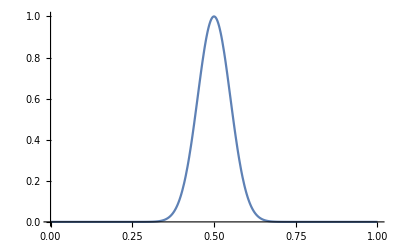

```mathematica
f[x_]:=ⅇ^(-1/2((x-0.5)/0.05)^2)
Plot[f[x],{x,0,1}, PlotRange->{0,1}]
```

```mathematica
f[0]
f[0.5]
f[1]
```

1.92875×10^-22

1.

1.92875×10^-22

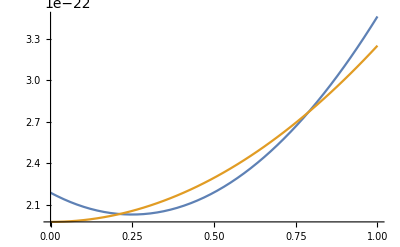

```mathematica
parabvalsf={2.1892726883626096*10^-22,3.459262649167623*10^-22,-2.5328063276163151*10^-22};
f[χ_]:= parabvalsf[[1]] + (parabvalsf[[2]]-parabvalsf[[1]] + parabvalsf[[3]])χ - parabvalsf[[3]] χ^2

parabvalsg={1.9788032938940600*10^-022, 3.2487932546990735*10^-022,-1.2699899608050177*10^-022};
g[χ_]:= parabvalsg[[1]] + (parabvalsg[[2]]-parabvalsg[[1]] + parabvalsg[[3]])χ - parabvalsg[[3]] χ^2


Plot[{f[χ],g[χ]},{χ,0,1}]
```

```mathematica
FindMinimum[g[χ]×10^22,{χ,0}]
```

{1.9796,{χ→0.332703}}

```mathematica
g[0.3327033450045631]
```

1.9796×10^-22

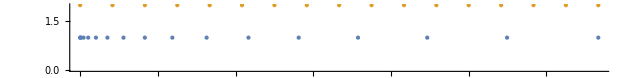

```mathematica
NumberLinePlot[{grid1,grid2}]
```

```mathematica
grid1
grid2
```

{0.,0.000244141,0.00195313,0.0065918,0.015625,0.0305176,0.0527344,0.0837402,0.125,0.177979,0.244141,0.324951,0.421875,0.536377,0.669922,0.823975,1.}

{0.,0.0625,0.125,0.1875,0.25,0.3125,0.375,0.4375,0.5,0.5625,0.625,0.6875,0.75,0.8125,0.875,0.9375,1.}

```mathematica
f[x_]:=(16/9)(x-1/4)^2
```

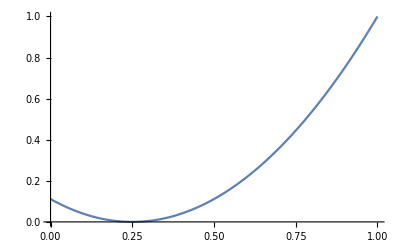

```mathematica
Plot[f[x],{x,0,1}]
```

```mathematica
ubnd=Integrate[f[x],{x,0,1}]+0.0
mass1=Integrate[f[x],{x,0,1/8}]+0.0;
mass2=Integrate[f[x],{x,1/8,6/8}]+0.0;
mass3=Integrate[f[x],{x,6/8,8/8}]+0.0;
dens2 = (5/8)^-1 mass2
dens3 = (2/8)^-1 mass3;
dens3diff=dens3-ubnd;
mass3diff = (2/8)dens3diff;
mass3 = mass3 - mass3diff;
mass2 = mass2+mass3diff;
dens2 = (5/8)^-1 mass2
dens3 = (2/8)^-1 mass3;
```

0.259259

0.12037

0.298148

```mathematica
dens[x_] := 3/4-1/2 x^2
```

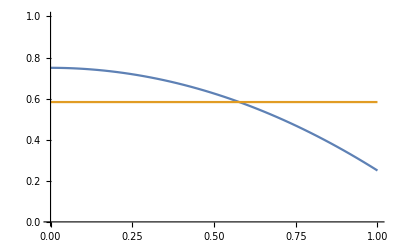

```mathematica
Plot[{dens[x],Integrate[dens[y],{y,0,1.}]},{x,0,1},PlotRange->{{0,1},{0,1}}]
```

```mathematica
Manipulate[{1./a Integrate[dens[x],{x,0,a}],1./(b-a)Integrate[dens[x],{x,a,b}],1./(1-b)Integrate[dens[x],{x,b,1}]},{a,0.01,1,0.01},{b,a+0.01,1.001,0.01}]
```

```mathematica
Manipulate[{Integrate[dens[x],{x,0,a}],Integrate[dens[x],{x,a,b}],Integrate[dens[x],{x,b,1}]},{a,0.01,1,0.01},{b,a+0.01,1.001,0.01}]
```

```mathematica
Integrate[dens[x],{x,0,1.}]
```

0.583333

```mathematica
cub_sqr
```

```mathematica
off
```

```mathematica
off, boundaries constant
```

```mathematica
off, mass borrowing
```

```mathematica
q_alg = 11
```

```mathematica
{694790.759510369,732134.094725595,770856.571210404,810989.850403089,852566.069170578,895617.848007448,940178.299388709,986281.036272797,1033960.18075569,1083250.37286667,1134186.77949842,1186805.10345630,1241141.59261379,1297233.04915419,1355116.83887951,1414830.90056578,1476413.75534269,1539904.51607543,1605342.89673014,1672769.22170112}
```

```mathematica
q_alg = 12
```

```mathematica
{694790.759510251,732134.094725712,770856.571210404,810989.850403089,852566.069170578,895617.848007448,940178.299388709,986281.036272797,1033960.18075569,1083250.37286667,1134186.77949842,1186805.10345630,1241141.59261379,1297233.04915419,1355116.83887951,1414830.90056578,1476413.75534269,1539904.51607543,1605342.89673014,1672769.22170112}
```

```mathematica
q_alg = 21
```

```mathematica
{694790.759510251,732134.094725712,770856.571210404,810989.850403089,852566.069170578,895617.848007448,940178.299388709,986281.036272797,1033960.18075569,1083250.37286667,1134186.77949842,1186805.10345630,1241141.59261379,1297233.04915419,1355116.83887951,1414830.90056578,1476413.75534269,1539904.51607543,1605342.89673014,1672769.22170112}
```

```mathematica
q_alg = 22
```

```mathematica
{694790.759510251,732134.094725712,770856.571210404,810989.850403089,852566.069170578,895617.848007448,940178.299388709,986281.036272797,1033960.18075569,1083250.37286667,1134186.77949842,1186805.10345630,1241141.59261379,1297233.04915419,1355116.83887951,1414830.90056578,1476413.75534269,1539904.51607543,1605342.89673014,1672769.22170112}
```

```mathematica
{694790.759510251,732134.094725712,770856.571210404,810989.850403089,852566.069170578,895617.848007448,940178.299388709,986281.036272797,1033960.18075569,1083250.37286667,1134186.77949842,1186805.10345630,1241141.59261379,1297233.04915419,1355116.83887951,1414830.90056578,1476413.75534269,1539904.51607543,1605342.89673014,1672769.22170112}-{694790.759510369,732134.094725595,770856.571210404,810989.850403089,852566.069170578,895617.848007448,940178.299388709,986281.036272797,1033960.18075569,1083250.37286667,1134186.77949842,1186805.10345630,1241141.59261379,1297233.04915419,1355116.83887951,1414830.90056578,1476413.75534269,1539904.51607543,1605342.89673014,1672769.22170112}
```

{-1.18045×10^-7,1.16997×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Cos[ArcSin[1/(√6)]]
```

√(5/6)

```mathematica
6^2*2
```

72

```mathematica
(25π √5)/72.
```

2.43917